```mathematica
Import["C:\\Users\\Juntao Yu\\Desktop\\LED\\BLEDUI.xlsx"]
```

```mathematica
data1={{10.,2.97},{11.,2.98},{12.,3.},{13.,3.01},{14.,3.02},{15.,3.03},{16.5,3.05},{18.,3.06},{20.,3.08},{22.,3.1},{24.,3.12},{25.4,3.14},{27.,3.13},{28.4,3.15},{30.,3.17},{31.5,3.18},{32.9,3.18},{34.,3.19}};
```

```mathematica
Import["C:\\Users\\Juntao Yu\\Desktop\\LED\\BLEDIL.xlsx"]
```

```mathematica
data2={{10.,0.48},{11.,0.508},{12.,0.543},{13.,0.579},{14.,0.604},{15.,0.637},{16.5,0.685},{18.,0.722},{20.,0.772},{22.,0.828},{24.,0.874},{25.4,0.913},{27.,0.938},{28.4,0.974},{30.,1.004},{31.5,1.036},{32.9,1.061},{34.,1.084}};
```

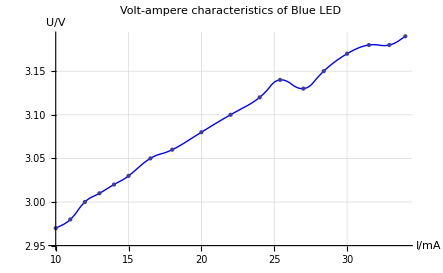

```mathematica
Show[gra1=ListLinePlot[data1,Joined-> True,InterpolationOrder->2,PlotStyle->Blue,AxesLabel->{"I/mA","U/V"},PlotLabel->"Volt-ampere characteristics of Blue LED",GridLines->Automatic],ListPlot[data1]]
```

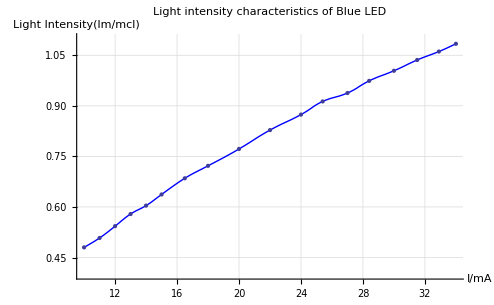

```mathematica
Show[gra2=ListLinePlot[data2,Joined-> True,InterpolationOrder->2,PlotStyle->Blue,AxesLabel->{"I/mA","Light Intensity(lm/mcl)"},PlotLabel->"Light intensity characteristics of Blue LED",GridLines->Automatic],ListPlot[data2],PlotRange->{0.4,1.1}]
```